# Frequency-dependent selection and global change -- thermal resilience of pigeons and other species with plumage polymorphism

First we consider a two allele model (see Endler 1988; Thompson 1984). Under this model, two alleles contribute color polymorphism and fitness (W) has both frequency-dependent and directional components, with S determining directional selection on the morph and f being the frequency of the allele.

```mathematica
W[S_,s_,f_]:=S+s*f
```

Under this model, if one allele is recessive and the recessive allele’s frequency is q, then the equilibrium frequency can be found by assuming HW equilibrium and solving for q (qsq represents q^2).

```mathematica
Solve[{SA +sA*(1-qsq)==Sa+sa*qsq},qsq]
```

{{qsq→(sA-Sa+SA)/(sa+sA)}}

This equilibrium can be stable or unstable. Stability is assessed by obtaining the single generation change in q and taking it’s derivative around the equilibrium q.

```mathematica
δq[q_,Sa_,sa_,SA_,sA_]:=-q+(q^2* W[Sa,sa,q^2]+ q *(1-q)*W[SA,sA,1-q^2])/(q^2* W[Sa,sa,q^2]+(1-q^2)*W[SA,sA,1-q^2])
```

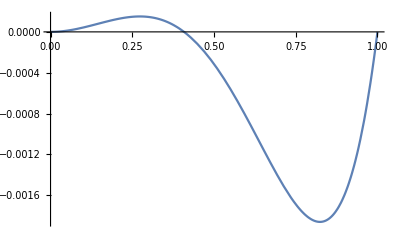

```mathematica
Plot[δq[q,0.995,-0.02,1.00,-0.01],{q,0,1}]
```

Thompson 1984 shows that the equilibrium is stable under the condition that sA + sa < W/[p*q^3]. At the equilibrium frequency,

```mathematica
δqEq[sa_,Sa_,sA_,SA_]:=δq[((sA-Sa+SA)/(sa+sA))^(1/2),Sa,sa,SA,sA]
FullSimplify[δqEq[sA,Sa,sA,SA]]
```

0

```mathematica
FullSimplify[D[δq[q,Sa,sa,SA,sA],q]]
```

-((q (2 q^4 sA (sa+sA)+q^7 (sa+sA)^2-4 q^2 (sa+sA) (sA+SA)+2 (sA+SA) (sA-Sa+SA)-3 q (sA+SA) (sA-Sa+SA)-q^5 (sa+sA) (5 sA-2 Sa+2 SA)+q^3 (7 sA^2+(Sa-SA)^2+5 sa (sA+SA)+sA (-3 Sa+8 SA))))/(sA+q^4 (sa+sA)+q^2 (-2 sA+Sa-SA)+SA)^2)

```mathematica
Dδq[q_,Sa_,sa_,SA_,sA_]:= -((q (2 q^4 sA (sa+sA)+q^7 (sa+sA)^2-4 q^2 (sa+sA) (sA+SA)+2 (sA+SA) (sA-Sa+SA)-3 q (sA+SA) (sA-Sa+SA)-q^5 (sa+sA) (5 sA-2 Sa+2 SA)+q^3 (7 sA^2+(Sa-SA)^2+5 sa (sA+SA)+sA (-3 Sa+8 SA))))/(sA+q^4 (sa+sA)+q^2 (-2 sA+Sa-SA)+SA)^2)
```

```mathematica
FullSimplify[Dδq[((sA-Sa+SA)/(sa+sA))^(1/2),Sa,sa,SA,sA]]
```

-(2 (sa+sA)^2 ((sA-Sa+SA)/(sa+sA))^(3/2) (-1+√((sA-Sa+SA)/(sa+sA))))/(sA Sa+sa (sA+SA))

```mathematica
FullSimplify[(sa+sA)/(sA Sa+sa (sA+SA))]
```

(sa+sA)/(sA Sa+sa (sA+SA))

```mathematica
FullSimplify[((sA-Sa+SA)/(sa+sA))*W[Sa,sa,((sA-Sa+SA)/(sa+sA))]+(1-(sA-Sa+SA)/(sa+sA))*W[Sa,sa,((sA-Sa+SA)/(sa+sA))]]
```

(sA Sa+sa (sA+SA))/(sa+sA)

```mathematica
DδqEq[Sa_,sa_,SA_,sA_]:=-(2 (sa+sA)^2 ((sA-Sa+SA)/(sa+sA))^(3/2) (-1+√((sA-Sa+SA)/(sa+sA))))/(sA Sa+sa (sA+SA))
```

This implies that stability of the equilibrium is achieved when this quantity is greater than -2 and less than 0 (see Thompson 1984).

Suppose that differences in Sa and SA are small, as might be the case when the per-day fitness cost of being above a thermal maximum is very small. Under these conditions, we can approximate the equation as follows, where replace :

```mathematica
FullSimplify[-(2 (sa+sA)^2 ((sA-Sa+SA)/(sa+sA))^(3/2) (-1+√((sA-Sa+SA)/(sa+sA))))/(SA(sA+sa))]
```

-(2 (sa+sA) ((sA-Sa+SA)/(sa+sA))^(3/2) (-1+√((sA-Sa+SA)/(sa+sA))))/SA

```mathematica
DδqEqApprox[Sa_,sa_,SA_,sA_]:=-(2 (sa+sA) ((sA-Sa+SA)/(sa+sA))^(3/2) (-1+√((sA-Sa+SA)/(sa+sA))))/SA
```

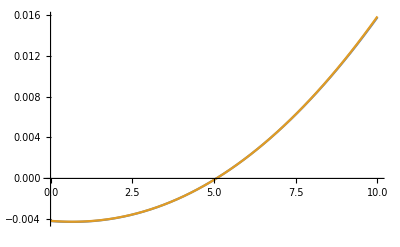

```mathematica
Plot[{DδqEq[(1-0.002)^d,-0.01,(1-0.002)^(2*d),-0.01],DδqEqApprox[(1-0.002)^d,-0.01,(1-0.002)^(2*d),-0.01]},{d,0,10}]
```

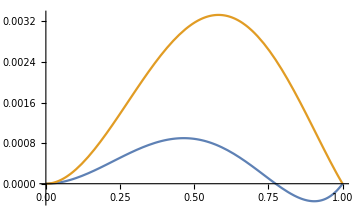

```mathematica
Plot[{δq[q,(1-0.002)^2,-0.01,(1-0.002)^(3),-0.01],δq[q,(1-0.002)^2,-0.01,(1-0.002)^(12),-0.01]},{q,0,1}]
```

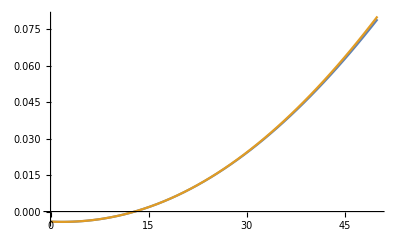

```mathematica
Plot[{DδqEq[(1-0.002)^d,-0.01,(1-0.002)^(1.4d),-0.01],DδqEqApprox[(1-0.002)^d,-0.01,(1-0.002)^(1.4d),-0.01]},{d,0,50}]
```

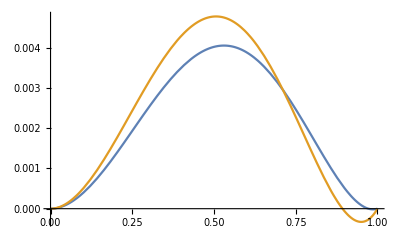

```mathematica
Plot[{δq[q,(1-0.02)^40,-0.01,(1-0.02)^(41),-0.01],δq[q,(1-0.02)^60,-0.01,(1-0.02)^(61),-0.01]},{q,0,1}]
```

We consider now a system in which the directional component is given by thermal properties of plumage coloration. For each day above critical temperature Ta, individuals with coloration a suffer a fitness cost of (1-S), while individuals of type A suffer a cost with the same functional form but at a different temperature threshold TA. Thus, we replace S in the first equation with (1-S)^d, where d is the number of days of the year that exceed the temperature threshold.

```mathematica
W[S_,s_,f_,d_]:=(1-S)^d+s*f
```

Supposing that the number of days per year that exceed a given temperature threshold is approximately constant over years, the model is effectively unchanged, but we replace SA and Sa with (1-S)^dA and (1-S)^da.  Supposing that fitness cost is small, we can approximate this with (1-S dA) and (1-S da). Now we can study how changes in temp profile might affect stability of plumage coloration.

```mathematica
qsq <- (sA - (1-S*da)+(1-S*dA))/(sa+sA)
```

so

```mathematica
qsq <- (sA + S*(da-dA))/(sa+sA)
```

This is a feasible equilibrium so long as sA and sa are both positive (i.e., fitness decreases when frequency increases, as is expected in our model) and S*(da-dA) is greater than -sA. note that since dA represents the number of days above the threshold for the darker phenotype, dA > da by definition, so this term S*(da-dA) is always negative in this model.

Equilibrium frequency and stability -- how do they change as (da-dA) increases?

## Pigeon Model

We now consider a three allele model motivated by the genetics of coloration in pigeons (https://learn.genetics.utah.edu/content/pigeons/color). We solve for the equilibrium frequencies under this model.

```mathematica
FullSimplify[Solve[{W[SBA,sBA,(p^2)/2+p*q+p*(1-(p+q))+p/2]== W[SBP,sBP,q^2/2+q*(1-(p+q))+q/2], W[SBA,sBA,(p^2)/2+p*q+p*(1-(p+q))+p/2]==W[Sb,sb,((1-(p+q))^2)/2+(1-(p+q))/2]},{p,q}]]
```

{{p→3/2-(√((-8 Sb+9 sBA+8 SBA) sBP+sb (9 sBA+8 SBA+sBP-8 SBP)))/(2 √(sBA sBP+sb (sBA+sBP))),q→1/(2 sBA sBP+2 sb (sBA+sBP))(√(sBA sBP+sb (sBA+sBP)) √((-8 Sb+9 sBA+8 SBA) sBP+sb (9 sBA+8 SBA+sBP-8 SBP))-√((sBA sBP+sb (sBA+sBP)) (9 sBA sBP+8 SBA sBP+sb (sBA+sBP)-8 Sb (sBA+sBP)+8 sBA SBP)))},{p→3/2-(√((-8 Sb+9 sBA+8 SBA) sBP+sb (9 sBA+8 SBA+sBP-8 SBP)))/(2 √(sBA sBP+sb (sBA+sBP))),q→1/(2 sBA sBP+2 sb (sBA+sBP))(√(sBA sBP+sb (sBA+sBP)) √((-8 Sb+9 sBA+8 SBA) sBP+sb (9 sBA+8 SBA+sBP-8 SBP))+√((sBA sBP+sb (sBA+sBP)) (9 sBA sBP+8 SBA sBP+sb (sBA+sBP)-8 Sb (sBA+sBP)+8 sBA SBP)))},{p→1/2 (3+(√((-8 Sb+9 sBA+8 SBA) sBP+sb (9 sBA+8 SBA+sBP-8 SBP)))/(√(sBA sBP+sb (sBA+sBP)))),q→-((√(sBA sBP+sb (sBA+sBP)) √((-8 Sb+9 sBA+8 SBA) sBP+sb (9 sBA+8 SBA+sBP-8 SBP))+√((sBA sBP+sb (sBA+sBP)) (9 sBA sBP+8 SBA sBP+sb (sBA+sBP)-8 Sb (sBA+sBP)+8 sBA SBP)))/(2 (sBA sBP+sb (sBA+sBP))))},{p→1/2 (3+(√((-8 Sb+9 sBA+8 SBA) sBP+sb (9 sBA+8 SBA+sBP-8 SBP)))/(√(sBA sBP+sb (sBA+sBP)))),q→1/(2 sBA sBP+2 sb (sBA+sBP))(-√(sBA sBP+sb (sBA+sBP)) √((-8 Sb+9 sBA+8 SBA) sBP+sb (9 sBA+8 SBA+sBP-8 SBP))+√((sBA sBP+sb (sBA+sBP)) (9 sBA sBP+8 SBA sBP+sb (sBA+sBP)-8 Sb (sBA+sBP)+8 sBA SBP)))}}

## Model of gamma distributed tMax and temp change

```mathematica
DtMax[x_,α_,β_]:=((β^α)/Gamma[α])*x^(α-1)*ⅇ^(-β x)
```

Let’s suppose that under climate change, the mean shifts by δ per year, but variance remains unchanged. Then 
	α1/β1 = α/β + δ, α1/β1^2 = α/β^2,

```mathematica
Solve[{α1/β1==α/β+t δ,α1/β1^2==α/β^2},{α1,β1}]
```

{{α1→(α+t β δ)^2/α,β1→(β (α+t β δ))/α}}

We can now solve for the difference in the proportion of the distribution that is above tMax as a function of the tMax threshold (xi\T in the calculation below).

```mathematica
Integrate[DtMax[x,(α+β t δ)^2/α,(β (α+β t δ))/α],{x,xT,∞}]
```

ConditionalExpression[1/Gamma[(α+t β δ)^2/α]((β (α+t β δ))/α)^((α+t β δ)^2/α) (((β (α+t β δ))/α)^(-(α+t β δ)^2/α) Gamma[(α+t β δ)^2/α]+xT^((α+t β δ)^2/α) ((xT β (α+t β δ))/α)^(-(α+t β δ)^2/α) (-Gamma[(α+t β δ)^2/α]+Gamma[(α+t β δ)^2/α,(xT β (α+t β δ))/α])), Re[(β (α+t β δ))/α]>0&&((Im[xT]==0&&Re[xT]>0)||xT∉ℝ)]

```mathematica
FullSimplify[1/Gamma[(α+t β δ)^2/α]((β (α+t β δ))/α)^((α+t β δ)^2/α) (((β (α+t β δ))/α)^(-(α+t β δ)^2/α) Gamma[(α+t β δ)^2/α]+xT^((α+t β δ)^2/α) ((xT β (α+t β δ))/α)^(-(α+t β δ)^2/α) (-Gamma[(α+t β δ)^2/α]+Gamma[(α+t β δ)^2/α,(xT β (α+t β δ))/α]))]
```

1+(xT^((α+t β δ)^2/α) ((β (α+t β δ))/α)^((α+t β δ)^2/α) ((xT β (α+t β δ))/α)^(-(α+t β δ)^2/α) (-Gamma[(α+t β δ)^2/α]+Gamma[(α+t β δ)^2/α,(xT β (α+t β δ))/α]))/Gamma[(α+t β δ)^2/α]

```mathematica
TotalDgTMax[α_,β_,δ_,t_,xT_]:=1+(xT^((α+t β δ)^2/α) ((β (α+t β δ))/α)^((α+t β δ)^2/α) ((xT β (α+t β δ))/α)^(-(α+t β δ)^2/α) (-Gamma[(α+t β δ)^2/α]+Gamma[(α+t β δ)^2/α,(xT β (α+t β δ))/α]))/Gamma[(α+t β δ)^2/α]
```

```mathematica
DiffInDgTMax[α_,β_,δ_,t_,xT_,xi_]:= 365*(TotalDgTMax[α,β,δ,t,xT-xi]-TotalDgTMax[α,β,δ,t,xT])
```

Distribution of max temp with mean 84 and variance 267 (same as Phoenix empirical variation in 1944) and 0.32 degrees F per year (global increase rate).

```mathematica
Solve[{α/β == x,α/β^2 == y}, {α, β} ]
```

{{α→x^2/y,β→x/y}}

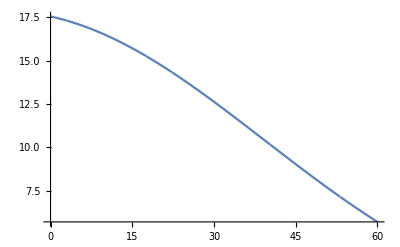

```mathematica
Plot[DiffInDgTMax[26.4,0.31,0.32,t,80,0.5],{t,0,60}]
```

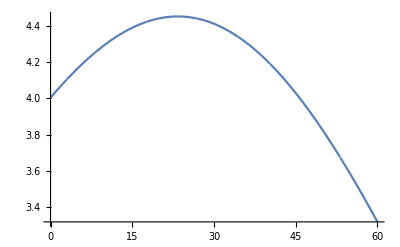

```mathematica
Plot[DiffInDgTMax[26.4,0.31,0.32,t,90,0.5],{t,0,60}]
```

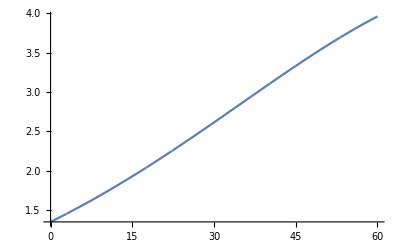

```mathematica
Plot[DiffInDgTMax[26.4,0.31,0.32,t,110,0.5],{t,0,60}]
```

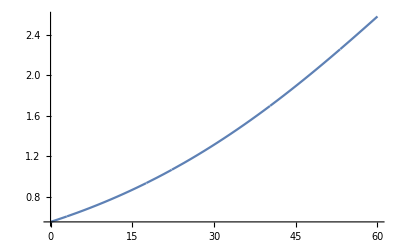

```mathematica
Plot[DiffInDgTMax[26.4,0.31,0.32,t,120,0.5],{t,0,60}]
```

```mathematica
(a/b) == 31.0
(a/b^2)^1/2 = 8.9
29.5 b/b^2 = 8.2
```

a/b==31.

Set::write: Tag Times in a/(2 b^2) is Protected.

8.9

Set::write: Tag Times in 29.5/b is Protected.

9.2

```mathematica
0.39*31
```

12.09

```mathematica
31/8.9
```

3.48315

```mathematica
3.48*31
```

107.88

```mathematica
107/(3.)
```

```mathematica
3.2*29.5
```

94.4

```mathematica
29.5*0.35
```

10.325

```mathematica
(10.33/0.35^2)^(1/2)
```

9.18295

```mathematica
(sA+(SA-SA))/(sa+sA)
```

```mathematica
Solve[q == (sA+(SA-Sa))/(sa+sA), sA]
```

{{sA→(-q sa-Sa+SA)/(-1+q)}}